```mathematica
<<SpaceMath`
```

SpaceMath v.1.0 | 
Documentation Centerpaclet:SpaceMath/tutorial/SpaceMathOverview | 
 | Examples
Cite |  | -Graphics-
Authors:
  ⊕ M. A. Arroyo-Ureña
 Facultad de Estudios Superiores-Cuautitlán, Universidad Nacional Autónoma de México
  ⊗ T. A. Valencia-Pérez
 Instituto de Física, Universidad Nacional Autónoma de México
 Contact us:	spacemathapp@gmail.com |

```mathematica
ghmumu[cα_,Zmumu_,u_]:= ((cα*mmu)/ vev)-((Sqrt[1-cα^2] Zmumu vev)/(Sqrt[2] u))
ghtaumu[cα_,Ztaumu_,u_]:= -((Sqrt[1-cα^2] Ztaumu vev)/(Sqrt[2] u))
gHmumu[cα_,Zmumu_,u_]:= ((√(1-cα^2)*mmu)/ vev)+(cα Zmumu vev)/(Sqrt[2] u)
gHtaumu[cα_,Ztaumu_,u_]:= (cα Ztaumu vev)/(Sqrt[2] u)
gAmumu[Zmumu_,u_]:= I*Zmumu /(Sqrt[2] u)
gAtaumu[Ztaumu_,u_]:= I*Ztaumu /(Sqrt[2] u)
```

```mathematica
muonAMDM[ghmumu[ca,0.001,u],ghtaumu[ca,Ztaumu,u],gHmumu[ca,0.001,u],gHtaumu[ca,Ztaumu,u],gAmumu[0.001,u],gAtaumu[Ztaumu,u],mH,500, ca, -1, 1,
u, 10,2000, Ztaumu,0.1,0.4,mH, 200,1000,10000]
```

{Null}

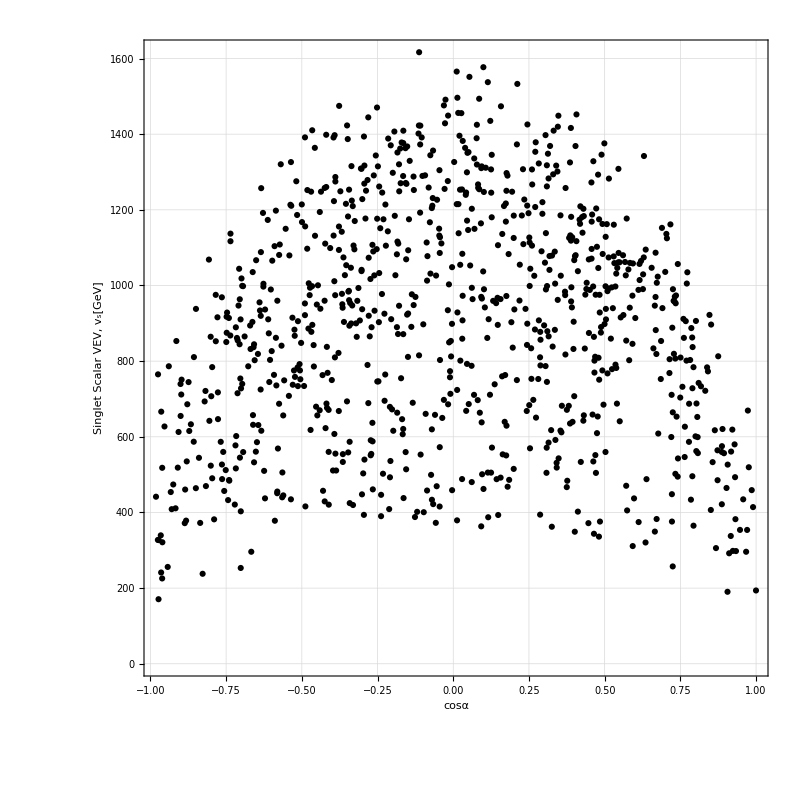

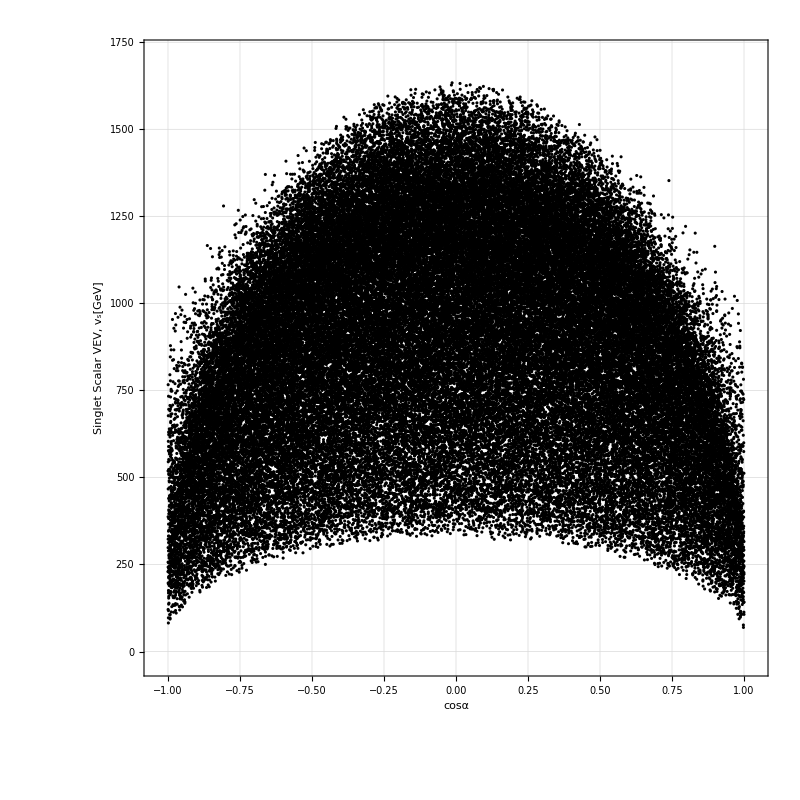

```mathematica
PlotMuonAMDM[1,2, "cosα", "Singlet Scalar VEV, v_s[GeV]"]
```